## Function Documentation

### This is a clickable list of functions and keywords that provide some documentation

```mathematica
?Mechanisms`*
```

```mathematica
?Mechanisms`geometry`*
```

```mathematica
?Mechanisms`rigidity`*
```

```mathematica
?Mechanisms`Origami`*
```

```mathematica
?Mechanisms`critical`*
```

## Creating mechanisms

Mechanisms are specified as

	head[ coordinates , cells ]

where coordinates are a list of vertex coordinates in either 2D or 3D and cells are of the form cell[ indices ].

Cells can have properties that are specified either as

	Property[ cell[ indices ], {property1 -> data1, property2 -> data2 , ...} ]

or

	cell[ indices , {property1 -> data1, ...} ]

### Linkage

A linkage can be specified as

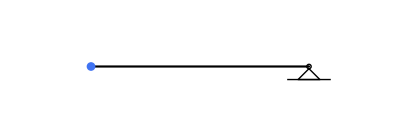

```mathematica
Linkage[{{0,0},{1,0}},{RigidBar[{1,2}],PinnedJoint[2]}]
```

You can include several sets of indices in each cell.

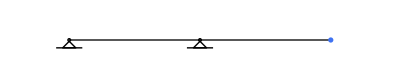

```mathematica
Linkage[{{0,0},{1,0},{2,0}},{RigidBar[{{1,2},{2,3}}],PinnedJoint[{1,2}]}]
```

### Origami

An origami mechanism is specified in the same way as a linkage, with the difference that vertices can be specified in 2D but the overall structure will still be three-dimensional.

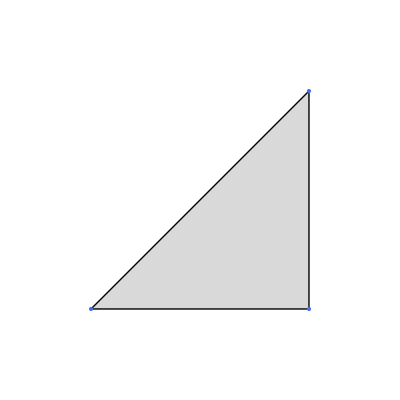

```mathematica
Origami[{{0,0},{1,0},{1,1}},{Face[{1,2,3}]}]
```

## Cell properties

To get a list of cells, you can call the function

```mathematica
DefaultCellProperties[]
```

{RigidBar,Spring,Face,ElasticTriangle,TorsionalFold,FreeJoint,PinnedJoint,AngleJoint}

without arguments.

Cell properties and their defaults can be found using the same function. The properties are all strings.

```mathematica
DefaultCellProperties[RigidBar]
```

{EquilibriumLength→Automatic,Stiffness→∞}

In addition, there are additional properties for all cells “Shape”, “Style”, and “Label” that can be used to specify the shape, style, and even a label for any cell.

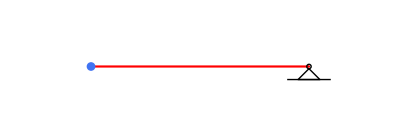

```mathematica
Linkage[{{0,0},{1,0}},{Property[RigidBar[{1,2}],"Style"->{Red}],PinnedJoint[2]}]
```

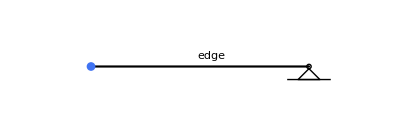

```mathematica
Linkage[{{0,0},{1,0}},{Property[RigidBar[{1,2}],"Label"->"edge"],PinnedJoint[2]}]
```

Note that properties that are unrecognized do not generate any errors and are just ignored.

```mathematica
Linkage[{{0,0},{1,0}},{Property[RigidBar[{1,2}],"Nothing"->"edge"],PinnedJoint[2]}]
```

-Graphics-

This means that properties can be inherited if the relevant cells are listed. If the property does not apply to a particular cell, ignoring it saves trouble of producing errors.

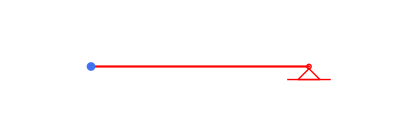

```mathematica
Linkage[{{0,0},{1,0}},{Property[ {RigidBar[{1,2}],PinnedJoint[2]}, {"Style"->Red,"Stiffness"->1}]} ]
```

## Extracting information and modifying mechanisms

The following are basic functions we can use to extract information from mechanisms or modify them.

### MechanismCells[]

```mathematica
?MechanismCells
```

This function returns raw information from a mechanism.

```mathematica
m=RandomOrigami[3];
```

```mathematica
MechanismCells[ m]
```

{FreeJoint,Face,RigidBar}

```mathematica
MechanismCells[m, _RigidBar]
```

{RigidBar[{{1,2},{2,3},{2,5},{3,4},{3,6},{4,1},{5,3},{5,7},{6,1},{6,4},{6,5},{6,7},{7,1},{7,2}}]}

```mathematica
MechanismCells[m,_RigidBar,"Stiffness"->_]
```

{RigidBar[{{1,2},{2,3},{2,5},{3,4},{3,6},{4,1},{5,3},{5,7},{6,1},{6,4},{6,5},{6,7},{7,1},{7,2}}]→{{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}},{EquilibriumLength→Automatic,Stiffness→∞,Shape→Automatic,Label→None,Style→{}}}}

### MechanismCellData[]

```mathematica
?MechanismCellData
```

This function is similar to MechanismCellList[] except it takes a pattern as input and replaces Automatic in the data with its actual value (except for “Shape”). The data is of the form

     cell[ {index1, index2, ...} ] -> <| “datatype1” -> {data1, ...} , ... |>
 
 where the data is presented in the same order as its corresponding index.

```mathematica
MechanismCellData[ RandomOrigami[2], _RigidBar]
```

{RigidBar[{{1,2},{1,6},{2,3},{3,4},{3,5},{3,6},{4,1},{5,1},{5,2},{6,4},{6,5}}]→<|EquilibriumLength→{1.41421,1.39985,1.41421,1.41421,1.37391,1.38482,1.41421,0.861526,0.591329,0.0329255,1.48145},Stiffness→{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},Shape→{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},Label→{None,None,None,None,None,None,None,None,None,None,None},Style→{{},{},{},{},{},{},{},{},{},{},{}}|>}

### MechanismVertices[], MechanismEdges[], InteriorEdges[], MechanismFaces[]

```mathematica
m=RandomOrigami[3];
```

```mathematica
MechanismVertices[m]
MechanismFaces[m]
MechanismEdges[m]
```

{1,2,3,4,5,6,7}

{{2,5,1},{3,7,2},{4,6,7},{4,7,3},{5,4,1},{6,4,5},{6,5,2},{7,6,2}}

{{1,2},{1,4},{1,5},{2,3},{2,5},{2,6},{2,7},{3,4},{3,7},{4,5},{4,6},{4,7},{5,6},{6,7}}

```mathematica
InteriorEdges[m]
```

{{1,5},{2,5},{2,6},{2,7},{3,7},{4,5},{4,6},{4,7},{5,6},{6,7}}

### MechanismConnectivity[]

```mathematica
?MechanismConnectivity
```

```mathematica
MechanismConnectivity["Methods"]
```

{{vertices,edges,faces}→{vertices,edges,faces,ordered faces,ordered edges}}

This function is used to work out what vertices, edges, and faces are connected to each other. It returns a list for each element of the left hand side of the rule and indicates all of the objects it is connected to on the right-hand side of the rule. To find all edges connected to each vertex, for example:

```mathematica
MechanismConnectivity[ m=RandomOrigami[3] , "vertices" -> "edges" ]
```

{{{1,2},{1,4},{1,6},{1,7}},{{2,3},{2,5},{2,7},{2,1}},{{3,4},{3,5},{3,2}},{{4,5},{4,6},{4,1},{4,3}},{{5,6},{5,7},{5,2},{5,3},{5,4}},{{6,7},{6,1},{6,4},{6,5}},{{7,1},{7,2},{7,5},{7,6}}}

If the object is oriented (see orientedQ[]) you can get the edges and faces in counterclockwise order.

```mathematica
MechanismConnectivity[ m , "vertices" -> "ordered edges" ]
```

{{{1,2},{1,7},{1,6}},{{2,3},{2,5},{2,7}},{{3,4},{3,5}},{{4,1},{4,6},{4,5}},{{5,2},{5,3},{5,4},{5,6},{5,7}},{{6,4},{6,1},{6,7},{6,5}},{{7,6},{7,1},{7,2},{7,5}}}

### ChangeCellData[]

```mathematica
?ChangeCellData
```

Make some random origami and extract the equilibrium lengths of all the edges.

```mathematica
MechanismCells[ f= RandomOrigami[3], _RigidBar]
```

{RigidBar[{{1,2},{1,7},{2,3},{2,5},{3,4},{3,6},{4,1},{4,6},{5,3},{5,6},{6,1},{6,7},{7,2},{7,5}}]}

Change all the length’s of rigidBar’s matching a particular pattern. Notice the order of the indices does not matter.

```mathematica
MechanismCells[ 
ChangeCellData[ f,RigidBar[{1,_}],"EquilibriumLength"->1 ],
 _RigidBar]
```

{RigidBar[{{1,2},{1,7},{2,3},{2,5},{3,4},{3,6},{4,1},{4,6},{5,3},{5,6},{6,1},{6,7},{7,2},{7,5}}]}

Add labels to a mechanism.

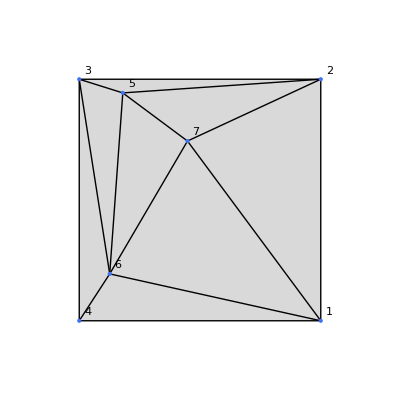

```mathematica
ChangeCellData[f,_FreeJoint,"Label"->"Index" ]
```

### DeleteCells[]

```mathematica
?DeleteCells
```

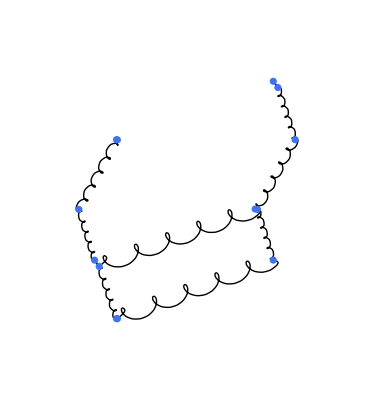

```mathematica
DeleteCells[ RandomCellNetwork[3], _[{1,_}]]
```

delete faces associated with vertex 1.

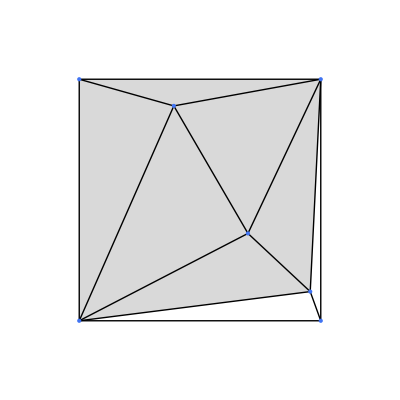

```mathematica
DeleteCells[ f=RandomOrigami[3],Face[{___,1,___}]]
```

Delete all cells associated with vertex 1. Note that the vertex itself remains.

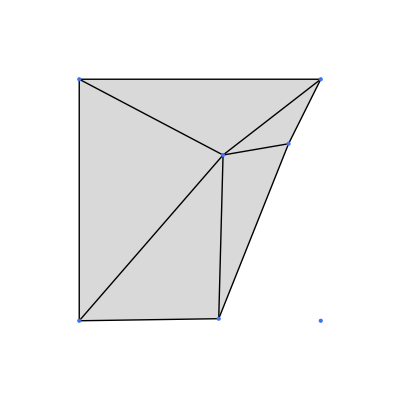

```mathematica
DeleteCells[ f=RandomOrigami[3],_[{___,1,___}]]
```

### AddCells[]

```mathematica
?AddCells
```

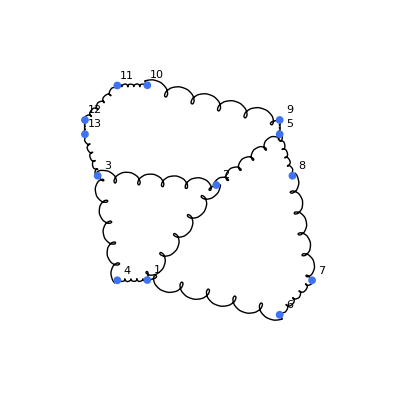

```mathematica
m=ChangeCellData[RandomCellNetwork[3],_FreeJoint,"Label"->"Index"]
```

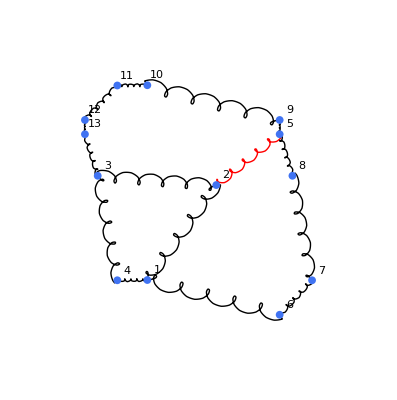

```mathematica
AddCells[ m, { Property[ Spring[{2,5}] , { "Style" -> Red } ]} ]
```

You can also overwrite existing parts of an mechanisms.

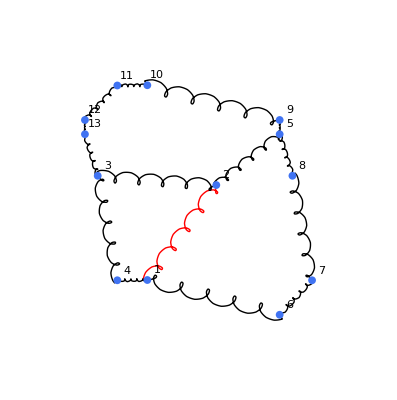

```mathematica
m2=AddCells[ m, { Property[ Spring[{2,1}] , { "Style" -> Red } ]} ]
```

```mathematica
MechanismCellData[m2,Spring[{2,1}]]
```

{Spring[{{2,1}}]→<|EquilibriumLength→{0.602591},Stiffness→{∞},Strain→{(#1-#2)/#2&},Shape→{Automatic},Label→{None},Style→{{RGBColor[1, 0, 0]}}|>}

### deleting and adding vertices with AddCells[] and DeleteVertices[]

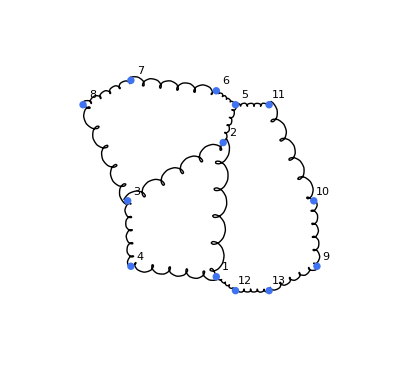

```mathematica
m=ChangeCellData[RandomCellNetwork[3],_FreeJoint,"Label"->"Index"]
```

You can add a vertex with addCell using the notation joint[ name -> position ] where label is a name to use to refer to the point and position are the coordinates of the new vertex. You then refer to the new vertex using its name.

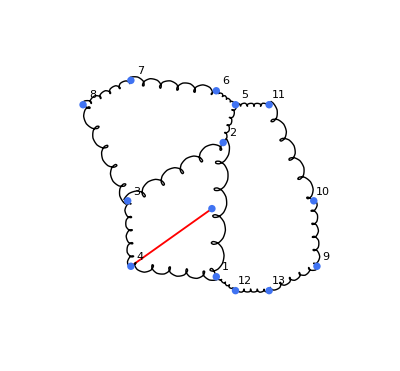

```mathematica
AddCells[ m, {FreeJoint[ "a"->{0,-1/4}], RigidBar[{"a",4},"Style"->Red]}]
```

deleteVertices[] deletes a vertex and everything connected to it.

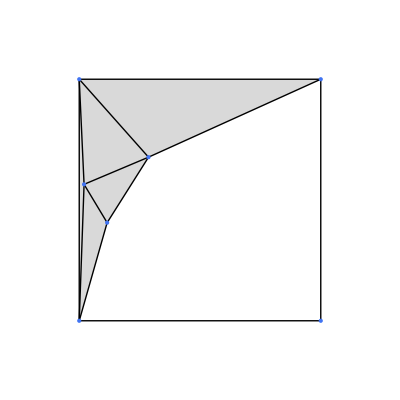

```mathematica
DeleteVertices[ m=RandomOrigami[4], {5}]
```

### SelectCells[]

```mathematica
?SelectCells
```

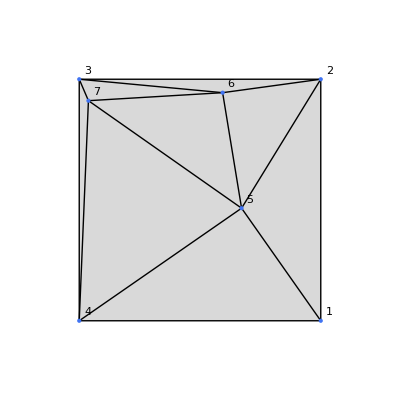

```mathematica
f=ChangeCellData[_FreeJoint,"Label"->"Index"]@RandomOrigami[3]
```

Select all the cells that are joined to vertex 1.

MeshRegion::pnset: Some or all of the properties specified in the Properties option could not be set.

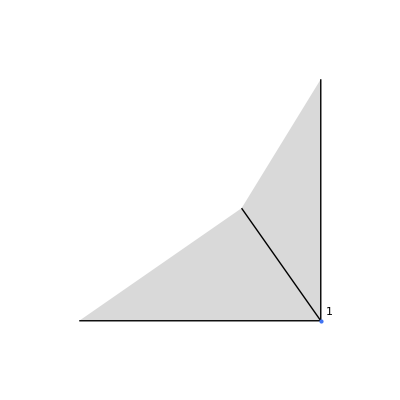

```mathematica
f2=ChangeCellData[_FreeJoint,"Label"->"Index"]@SelectCells[f,_[1]|_[{___,1,___}]]
```

```mathematica
MechanismCellData[f]
```

{FreeJoint[{1,2,3,4,5,6,7}]→<|Shape→{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},Label→{Index,Index,Index,Index,Index,Index,Index},Style→{{},{},{},{},{},{},{}}|>,Face[{{1,5,4},{2,5,1},{4,5,7},{5,2,6},{5,6,7},{6,2,3},{7,3,4},{7,6,3}}]→<|FaceStiffness→{0,0,0,0,0,0,0,0},Shape→{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},Label→{None,None,None,None,None,None,None,None},Style→{{},{},{},{},{},{},{},{}}|>,RigidBar[{{1,2},{2,3},{2,6},{3,4},{3,6},{3,7},{4,1},{4,5},{5,1},{5,2},{6,5},{6,7},{7,4},{7,5}}]→<|EquilibriumLength→{1.41421,1.41421,0.579996,1.41421,0.843269,0.136643,1.41421,1.15672,0.805929,0.886053,0.685346,0.787154,1.28974,1.09556},Stiffness→{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞},Shape→{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},Label→{None,None,None,None,None,None,None,None,None,None,None,None,None,None},Style→{{},{},{},{},{},{},{},{},{},{},{},{},{},{}}|>}

```mathematica
MechanismCellData[f2]
```

{FreeJoint[{1}]→<|Shape→{Automatic},Label→{Index},Style→{{}}|>,Face[{{1,5,4},{2,5,1}}]→<|FaceStiffness→{0,0},Shape→{Automatic,Automatic},Label→{None,None},Style→{{},{}}|>,RigidBar[{{1,2},{4,1},{5,1}}]→<|EquilibriumLength→{1.41421,1.41421,0.805929},Stiffness→{∞,∞,∞},Shape→{Automatic,Automatic,Automatic},Label→{None,None,None},Style→{{},{},{}}|>}

Keep all the rigid bars connected to vertex 1 but all the faces in the structure.

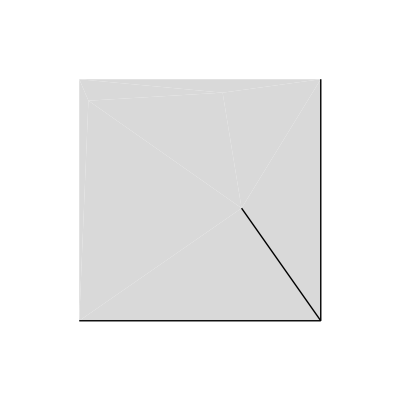

```mathematica
f2=SelectCells[f,Face[_]| RigidBar[{___,1,___}]]
```

### DisplaceVertices[]

```mathematica
?DisplaceVertices
```

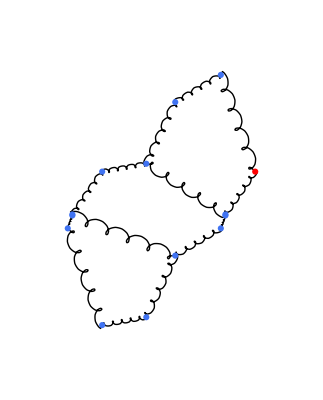
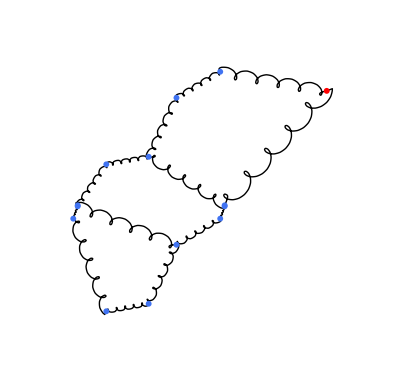

```mathematica
{
f=ChangeCellData[FreeJoint[1],"Style"->{Red,PointSize[0.029]}]@RandomCellNetwork[3],
DisplaceVertices[ f, {1->{0.5,0.5}} ]
}
```

```mathematica
DisplaceVertices[ RandomOrigami[2], RandomReal[ {-0.1,0.1}, {6,3}]]
```

-Graphics3D-

### SubdivideCell[]

```mathematica
?SubdivideCells
```

Create a vertex on an edge and displace it.

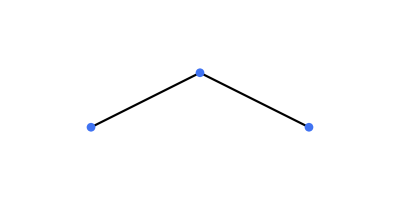

```mathematica
DisplaceVertices[{"a"->{0,1/4}}]@SubdivideCells[Linkage[ {{0,0},{1,0}}, {RigidBar[{1,2}]}],{{1,2}},"a"]
```

### Henneberg[]

Henneberg operations acting on a 2D linkage preserve the number of degrees of freedom (generically).

```mathematica
?Henneberg
```

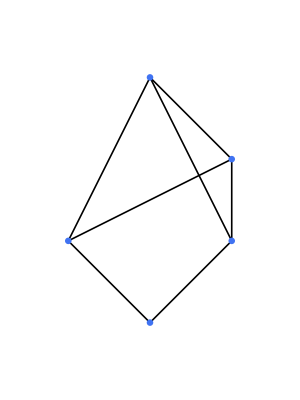

```mathematica
f2=Henneberg[2][ {1,2,"b"}, "a"->{1,1/2} ] @ Henneberg[1][ {1,2}, "c"->{1/2,-1/2} ] @ AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ Linkage[{{0,0},{1,0}},{RigidBar[{1,2}]}]
```

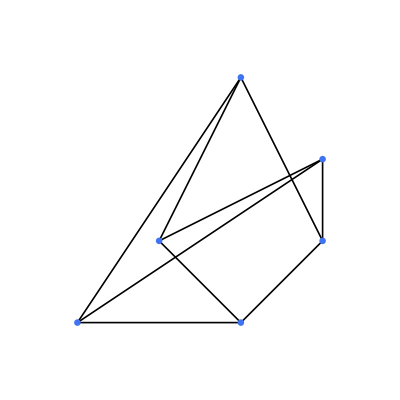

```mathematica
Henneberg[2][{-1/2,-1/2}] @ f2
```

### JoinMechanism[]

```mathematica
?JoinMechanism
```

```mathematica
JoinMechanism[ RandomOrigami[2], #+{0,0,1}& /@ RandomOrigami[3] ]
```

-Graphics3D-

Two vertices that are sufficiently close together will be merged. Use “overlapPrecision” to specify how close to operate this.

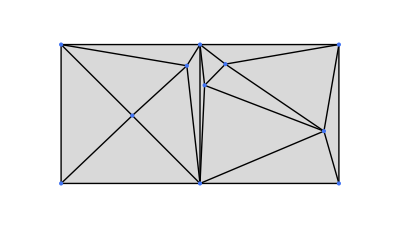

```mathematica
JoinMechanism[ RandomOrigami[2], #+{Sqrt[2],0,0}& /@ RandomOrigami[3] ]
```

## Rigidity

## MechanismCellData[]

```mathematica
?MechanismCellData
```

### Details

Cell data labeled Automatic is resolved into numbers for everything but graphics.

MechanismCellData[ Deformed[m, new positions] , ... ] is the same as MechanismCellData[m, ...] because MechanismCellData[] always uses the mechanism itself to resolve cells that have Automatic properties.

Data is returned as a list, with each element given by cell[ {i1,i2,...}] -> Association[ data1 -> {d1,d2,d3,...}, ... ]

### Basic examples

```mathematica
MechanismCellData[RandomOrigami[1]]
```

{FreeJoint[{1,2,3,4,5}]→<|Shape→{Automatic,Automatic,Automatic,Automatic,Automatic},Label→{None,None,None,None,None},Style→{{},{},{},{},{}}|>,Face[{{2,5,1},{5,2,3},{5,3,4},{5,4,1}}]→<|FaceStiffness→{0,0,0,0},Shape→{Automatic,Automatic,Automatic,Automatic},Label→{None,None,None,None},Style→{{},{},{},{}}|>,RigidBar[{{1,2},{2,3},{3,4},{3,5},{4,1},{4,5},{5,1},{5,2}}]→<|EquilibriumLength→{1.41421,1.41421,1.41421,1.08655,1.41421,1.20166,0.95313,0.803158},Stiffness→{∞,∞,∞,∞,∞,∞,∞,∞},Shape→{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic},Label→{None,None,None,None,None,None,None,None},Style→{{},{},{},{},{},{},{},{}}|>}

```mathematica
MechanismCellData[RandomOrigami[1],_FreeJoint]
```

{FreeJoint[{1,2,3,4,5}]→<|Shape→{Automatic,Automatic,Automatic,Automatic,Automatic},Label→{None,None,None,None,None},Style→{{},{},{},{},{}}|>}

## MechanismConstraintMap[]

```mathematica
?MechanismConstraintMap
```

### Details

cells with constraints are those that have an Infinite stiffness, including RigidBar, Spring, TorsionalFold, PinnedJoint, Face, and ElasticFace.

### Basic examples

```mathematica
MechanismConstraintMap[ RandomOrigami[1] ]
```

{-2.+(-VertexPosition[1,x]+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2+(-VertexPosition[1,z]+VertexPosition[2,z])^2,-0.669956+(-VertexPosition[1,x]+VertexPosition[5,x])^2+(-VertexPosition[1,y]+VertexPosition[5,y])^2+(-VertexPosition[1,z]+VertexPosition[5,z])^2,-2.+(-VertexPosition[2,x]+VertexPosition[3,x])^2+(-VertexPosition[2,y]+VertexPosition[3,y])^2+(-VertexPosition[2,z]+VertexPosition[3,z])^2,-2.+(-VertexPosition[3,x]+VertexPosition[4,x])^2+(-VertexPosition[3,y]+VertexPosition[4,y])^2+(-VertexPosition[3,z]+VertexPosition[4,z])^2,-2.+(VertexPosition[1,x]-VertexPosition[4,x])^2+(VertexPosition[1,y]-VertexPosition[4,y])^2+(VertexPosition[1,z]-VertexPosition[4,z])^2,-0.799334+(VertexPosition[2,x]-VertexPosition[5,x])^2+(VertexPosition[2,y]-VertexPosition[5,y])^2+(VertexPosition[2,z]-VertexPosition[5,z])^2,-1.43536+(VertexPosition[3,x]-VertexPosition[5,x])^2+(VertexPosition[3,y]-VertexPosition[5,y])^2+(VertexPosition[3,z]-VertexPosition[5,z])^2,-1.30598+(VertexPosition[4,x]-VertexPosition[5,x])^2+(VertexPosition[4,y]-VertexPosition[5,y])^2+(VertexPosition[4,z]-VertexPosition[5,z])^2}

```mathematica
MechanismConstraintMap[ Deformed[(m=RandomOrigami[1]) , RandomPositions[m] ]]
```

{0.846017,-0.441964,-0.326329,0.775949,-0.305395,0.653702,0.421088,0.753293}

To get constraints to a specific order, you can specify the order with an integer.

```mathematica
MechanismConstraintMap[ (m=RandomOrigami[1]) , 1 ]
```

{-2.+2 (-VertexDisplacement[1,x]+VertexDisplacement[2,x]) (-VertexPosition[1,x]+VertexPosition[2,x])+(-VertexPosition[1,x]+VertexPosition[2,x])^2+2 (-VertexDisplacement[1,y]+VertexDisplacement[2,y]) (-VertexPosition[1,y]+VertexPosition[2,y])+(-VertexPosition[1,y]+VertexPosition[2,y])^2+2 (-VertexDisplacement[1,z]+VertexDisplacement[2,z]) (-VertexPosition[1,z]+VertexPosition[2,z])+(-VertexPosition[1,z]+VertexPosition[2,z])^2,-2.+2 (-VertexDisplacement[2,x]+VertexDisplacement[3,x]) (-VertexPosition[2,x]+VertexPosition[3,x])+(-VertexPosition[2,x]+VertexPosition[3,x])^2+2 (-VertexDisplacement[2,y]+VertexDisplacement[3,y]) (-VertexPosition[2,y]+VertexPosition[3,y])+(-VertexPosition[2,y]+VertexPosition[3,y])^2+2 (-VertexDisplacement[2,z]+VertexDisplacement[3,z]) (-VertexPosition[2,z]+VertexPosition[3,z])+(-VertexPosition[2,z]+VertexPosition[3,z])^2,-3.61368+2 (-VertexDisplacement[2,x]+VertexDisplacement[5,x]) (-VertexPosition[2,x]+VertexPosition[5,x])+(-VertexPosition[2,x]+VertexPosition[5,x])^2+2 (-VertexDisplacement[2,y]+VertexDisplacement[5,y]) (-VertexPosition[2,y]+VertexPosition[5,y])+(-VertexPosition[2,y]+VertexPosition[5,y])^2+2 (-VertexDisplacement[2,z]+VertexDisplacement[5,z]) (-VertexPosition[2,z]+VertexPosition[5,z])+(-VertexPosition[2,z]+VertexPosition[5,z])^2,-2.+2 (-VertexDisplacement[3,x]+VertexDisplacement[4,x]) (-VertexPosition[3,x]+VertexPosition[4,x])+(-VertexPosition[3,x]+VertexPosition[4,x])^2+2 (-VertexDisplacement[3,y]+VertexDisplacement[4,y]) (-VertexPosition[3,y]+VertexPosition[4,y])+(-VertexPosition[3,y]+VertexPosition[4,y])^2+2 (-VertexDisplacement[3,z]+VertexDisplacement[4,z]) (-VertexPosition[3,z]+VertexPosition[4,z])+(-VertexPosition[3,z]+VertexPosition[4,z])^2,-2.+2 (VertexDisplacement[1,x]-VertexDisplacement[4,x]) (VertexPosition[1,x]-VertexPosition[4,x])+(VertexPosition[1,x]-VertexPosition[4,x])^2+2 (VertexDisplacement[1,y]-VertexDisplacement[4,y]) (VertexPosition[1,y]-VertexPosition[4,y])+(VertexPosition[1,y]-VertexPosition[4,y])^2+2 (VertexDisplacement[1,z]-VertexDisplacement[4,z]) (VertexPosition[1,z]-VertexPosition[4,z])+(VertexPosition[1,z]-VertexPosition[4,z])^2,-0.0142543+2 (-VertexDisplacement[4,x]+VertexDisplacement[5,x]) (-VertexPosition[4,x]+VertexPosition[5,x])+(-VertexPosition[4,x]+VertexPosition[5,x])^2+2 (-VertexDisplacement[4,y]+VertexDisplacement[5,y]) (-VertexPosition[4,y]+VertexPosition[5,y])+(-VertexPosition[4,y]+VertexPosition[5,y])^2+2 (-VertexDisplacement[4,z]+VertexDisplacement[5,z]) (-VertexPosition[4,z]+VertexPosition[5,z])+(-VertexPosition[4,z]+VertexPosition[5,z])^2,-1.68396+2 (VertexDisplacement[1,x]-VertexDisplacement[5,x]) (VertexPosition[1,x]-VertexPosition[5,x])+(VertexPosition[1,x]-VertexPosition[5,x])^2+2 (VertexDisplacement[1,y]-VertexDisplacement[5,y]) (VertexPosition[1,y]-VertexPosition[5,y])+(VertexPosition[1,y]-VertexPosition[5,y])^2+2 (VertexDisplacement[1,z]-VertexDisplacement[5,z]) (VertexPosition[1,z]-VertexPosition[5,z])+(VertexPosition[1,z]-VertexPosition[5,z])^2,-1.94398+2 (VertexDisplacement[3,x]-VertexDisplacement[5,x]) (VertexPosition[3,x]-VertexPosition[5,x])+(VertexPosition[3,x]-VertexPosition[5,x])^2+2 (VertexDisplacement[3,y]-VertexDisplacement[5,y]) (VertexPosition[3,y]-VertexPosition[5,y])+(VertexPosition[3,y]-VertexPosition[5,y])^2+2 (VertexDisplacement[3,z]-VertexDisplacement[5,z]) (VertexPosition[3,z]-VertexPosition[5,z])+(VertexPosition[3,z]-VertexPosition[5,z])^2}

### Options

#### CellPattern

Only list constraints for cells that match a particular pattern.

```mathematica
MechanismConstraintMap[ RandomOrigami[1], CellPattern -> RigidBar[{1,_}] ]
```

{-2.+(-VertexPosition[1,x]+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2+(-VertexPosition[1,z]+VertexPosition[2,z])^2,-0.0962881+(-VertexPosition[1,x]+VertexPosition[5,x])^2+(-VertexPosition[1,y]+VertexPosition[5,y])^2+(-VertexPosition[1,z]+VertexPosition[5,z])^2,-2.+(VertexPosition[1,x]-VertexPosition[4,x])^2+(VertexPosition[1,y]-VertexPosition[4,y])^2+(VertexPosition[1,z]-VertexPosition[4,z])^2}

#### Constraints

Add an additional constraint that is specified as an equation.

```mathematica
Last @ MechanismConstraintMap[ RandomOrigami[1], Constraints -> {VertexPosition[1,"x"] == 3}  ]
```

-3+VertexPosition[1,x]

VertexDisplacement[] can be used to specify that a vertex should not be displaced from its location.

```mathematica
Last @ MechanismConstraintMap[ RandomOrigami[1], Constraints -> {VertexDisplacement[1,"x"] == 0}  ]
```

-0.707107+VertexPosition[1,x]

#### ReduceLinearConstraints

Any linear constraints can be solved automatically and used to simplify the number of constraints that appear.

```mathematica
MechanismConstraintMap[ RandomOrigami[1], Constraints -> {VertexPosition[1,"x"] == 3}  , ReduceLinearConstraints -> True]
```

{-2.+(-3+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2+(-VertexPosition[1,z]+VertexPosition[2,z])^2,-2.+(-VertexPosition[2,x]+VertexPosition[3,x])^2+(-VertexPosition[2,y]+VertexPosition[3,y])^2+(-VertexPosition[2,z]+VertexPosition[3,z])^2,-0.381543+(-VertexPosition[2,x]+VertexPosition[5,x])^2+(-VertexPosition[2,y]+VertexPosition[5,y])^2+(-VertexPosition[2,z]+VertexPosition[5,z])^2,-2.+(-VertexPosition[3,x]+VertexPosition[4,x])^2+(-VertexPosition[3,y]+VertexPosition[4,y])^2+(-VertexPosition[3,z]+VertexPosition[4,z])^2,-0.939566+(-VertexPosition[3,x]+VertexPosition[5,x])^2+(-VertexPosition[3,y]+VertexPosition[5,y])^2+(-VertexPosition[3,z]+VertexPosition[5,z])^2,-2.+(3-VertexPosition[4,x])^2+(VertexPosition[1,y]-VertexPosition[4,y])^2+(VertexPosition[1,z]-VertexPosition[4,z])^2,-1.39511+(3-VertexPosition[5,x])^2+(VertexPosition[1,y]-VertexPosition[5,y])^2+(VertexPosition[1,z]-VertexPosition[5,z])^2,-1.95314+(VertexPosition[4,x]-VertexPosition[5,x])^2+(VertexPosition[4,y]-VertexPosition[5,y])^2+(VertexPosition[4,z]-VertexPosition[5,z])^2}

### Possible Issues

If an object has no Infinite stiffnesses, constraints may not appear. You can use ChangeCellData[] to set stiffnesses to Infinity where needed.

```mathematica
MechanismConstraintMap[ChangeCellData[  RandomCellNetwork[1] , _Spring, "Stiffness" -> 1 ] ]
```

{}

## MechanismEnergy[]

```mathematica
?MechanismEnergy
```

### Details

$DefaultMechanismStiffnesses[“Methods”] lists the cells that have default stiffnesses when their specified stiffness in Infinite.

```mathematica
$DefaultMechanismStiffnesses["Methods"]
```

{RigidBar,Spring,TorsionalFold,FreeJoint,Face,AngleJoint}

Use $DefaultMechanismStiffness[] to understand the relative magnitude of stiffnesses that are assumed.

```mathematica
$DefaultMechanismStiffnesses[RigidBar]
```

1

```mathematica
$DefaultMechanismStiffnesses[TorsionalFold]
```

1/10000

### Basic examples

```mathematica
MechanismEnergy[ RandomOrigami[1] ]
```

0.03125 (-2.+(-VertexPosition[1,x]+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2+(-VertexPosition[1,z]+VertexPosition[2,z])^2)^2+0.03125 (-2.+(-VertexPosition[2,x]+VertexPosition[3,x])^2+(-VertexPosition[2,y]+VertexPosition[3,y])^2+(-VertexPosition[2,z]+VertexPosition[3,z])^2)^2+0.03125 (-2.+(VertexPosition[1,x]-VertexPosition[4,x])^2+(VertexPosition[1,y]-VertexPosition[4,y])^2+(VertexPosition[1,z]-VertexPosition[4,z])^2)^2+0.03125 (-2.+(-VertexPosition[3,x]+VertexPosition[4,x])^2+(-VertexPosition[3,y]+VertexPosition[4,y])^2+(-VertexPosition[3,z]+VertexPosition[4,z])^2)^2+0.0392983 (-1.78348+(VertexPosition[1,x]-VertexPosition[5,x])^2+(VertexPosition[1,y]-VertexPosition[5,y])^2+(VertexPosition[1,z]-VertexPosition[5,z])^2)^2+0.0186728 (-2.58732+(VertexPosition[4,x]-VertexPosition[5,x])^2+(VertexPosition[4,y]-VertexPosition[5,y])^2+(VertexPosition[4,z]-VertexPosition[5,z])^2)^2+3.10636 (-0.200599+(-VertexPosition[2,x]+VertexPosition[5,x])^2+(-VertexPosition[2,y]+VertexPosition[5,y])^2+(-VertexPosition[2,z]+VertexPosition[5,z])^2)^2+0.123898 (-1.00444+(-VertexPosition[3,x]+VertexPosition[5,x])^2+(-VertexPosition[3,y]+VertexPosition[5,y])^2+(-VertexPosition[3,z]+VertexPosition[5,z])^2)^2

### Options

#### CellPattern

Only list constraints for cells that match a particular pattern.

```mathematica
MechanismEnergy[ RandomOrigami[1], CellPattern -> RigidBar[{1,_}] ]
```

0.03125 (-2.+(-VertexPosition[1,x]+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2+(-VertexPosition[1,z]+VertexPosition[2,z])^2)^2+0.03125 (-2.+(VertexPosition[1,x]-VertexPosition[4,x])^2+(VertexPosition[1,y]-VertexPosition[4,y])^2+(VertexPosition[1,z]-VertexPosition[4,z])^2)^2+0.544688 (-0.47905+(VertexPosition[1,x]-VertexPosition[5,x])^2+(VertexPosition[1,y]-VertexPosition[5,y])^2+(VertexPosition[1,z]-VertexPosition[5,z])^2)^2

#### Constraints

Add an additional constraint that is specified as an equation.

```mathematica
MechanismEnergy[ RandomOrigami[1], Constraints -> {VertexPosition[1,"x"] == 3}  ]
```

0.03125 (-2.+(-3+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2+(-VertexPosition[1,z]+VertexPosition[2,z])^2)^2+0.03125 (-2.+(-VertexPosition[2,x]+VertexPosition[3,x])^2+(-VertexPosition[2,y]+VertexPosition[3,y])^2+(-VertexPosition[2,z]+VertexPosition[3,z])^2)^2+0.03125 (-2.+(3-VertexPosition[4,x])^2+(VertexPosition[1,y]-VertexPosition[4,y])^2+(VertexPosition[1,z]-VertexPosition[4,z])^2)^2+0.03125 (-2.+(-VertexPosition[3,x]+VertexPosition[4,x])^2+(-VertexPosition[3,y]+VertexPosition[4,y])^2+(-VertexPosition[3,z]+VertexPosition[4,z])^2)^2+58.3477 (-0.0462853+(3-VertexPosition[5,x])^2+(VertexPosition[1,y]-VertexPosition[5,y])^2+(VertexPosition[1,z]-VertexPosition[5,z])^2)^2+0.0561914 (-1.49149+(VertexPosition[4,x]-VertexPosition[5,x])^2+(VertexPosition[4,y]-VertexPosition[5,y])^2+(VertexPosition[4,z]-VertexPosition[5,z])^2)^2+0.0387386 (-1.79632+(-VertexPosition[2,x]+VertexPosition[5,x])^2+(-VertexPosition[2,y]+VertexPosition[5,y])^2+(-VertexPosition[2,z]+VertexPosition[5,z])^2)^2+0.0118963 (-3.24152+(-VertexPosition[3,x]+VertexPosition[5,x])^2+(-VertexPosition[3,y]+VertexPosition[5,y])^2+(-VertexPosition[3,z]+VertexPosition[5,z])^2)^2

VertexDisplacement[] can be used to specify that a vertex should not be displaced from its location.

```mathematica
MechanismEnergy[ RandomOrigami[1], Constraints -> {VertexDisplacement[1,"x"] == 0}  ]
```

0.03125 (-2.+(-0.707107+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2+(-VertexPosition[1,z]+VertexPosition[2,z])^2)^2+0.03125 (-2.+(-VertexPosition[2,x]+VertexPosition[3,x])^2+(-VertexPosition[2,y]+VertexPosition[3,y])^2+(-VertexPosition[2,z]+VertexPosition[3,z])^2)^2+0.03125 (-2.+(0.707107-VertexPosition[4,x])^2+(VertexPosition[1,y]-VertexPosition[4,y])^2+(VertexPosition[1,z]-VertexPosition[4,z])^2)^2+0.03125 (-2.+(-VertexPosition[3,x]+VertexPosition[4,x])^2+(-VertexPosition[3,y]+VertexPosition[4,y])^2+(-VertexPosition[3,z]+VertexPosition[4,z])^2)^2+0.096218 (-1.1398+(VertexPosition[3,x]-VertexPosition[5,x])^2+(VertexPosition[3,y]-VertexPosition[5,y])^2+(VertexPosition[3,z]-VertexPosition[5,z])^2)^2+1.49658 (-0.289005+(VertexPosition[4,x]-VertexPosition[5,x])^2+(VertexPosition[4,y]-VertexPosition[5,y])^2+(VertexPosition[4,z]-VertexPosition[5,z])^2)^2+0.0747288 (-1.29334+(-0.707107+VertexPosition[5,x])^2+(-VertexPosition[1,y]+VertexPosition[5,y])^2+(-VertexPosition[1,z]+VertexPosition[5,z])^2)^2+0.02719 (-2.14413+(-VertexPosition[2,x]+VertexPosition[5,x])^2+(-VertexPosition[2,y]+VertexPosition[5,y])^2+(-VertexPosition[2,z]+VertexPosition[5,z])^2)^2

#### ConstraintModulus

```mathematica
MechanismEnergy[ Linkage[{{0,0},{1,0}},{RigidBar[{1,2}]}], Constraints-> {VertexDisplacement[1,"x"]^2},ConstraintModulus -> 3]
```

3/2 VertexPosition[1,x]^4+1/8 (-1+(-VertexPosition[1,x]+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2)^2

### Possible Issues

Linear constraints are automatically solved and simplified so they do not appear in the energy unnecessarily.

```mathematica
MechanismEnergy[ Linkage[{{0,0},{1,0}},{RigidBar[{1,2}]}], Constraints-> {VertexPosition[1,"x"]==3}]
```

1/8 (-1+(-3+VertexPosition[2,x])^2+(-VertexPosition[1,y]+VertexPosition[2,y])^2)^2

## MinimizeMechanismEnergy[]

```mathematica
?MinimizeMechanismEnergy
```

### Basic examples

```mathematica
MinimizeMechanismEnergy[ m = Origami[{{0,0},{1,0},{1,1},{2,0}},{TorsionalFold[{2,3},"Angle"-> Pi/2], Face[{1,2,3}],Face[{4,2,3}] }]]
```

{8.25168×10^-22,{{0.29967,-0.0724032,0.305112},{0.987567,0.0901874,-0.40225},{0.999487,1.06211,-0.167257},{1.71328,-0.0798954,0.264395}}}

### Options

#### InitialPositions

You can specify an initial position explicitly with

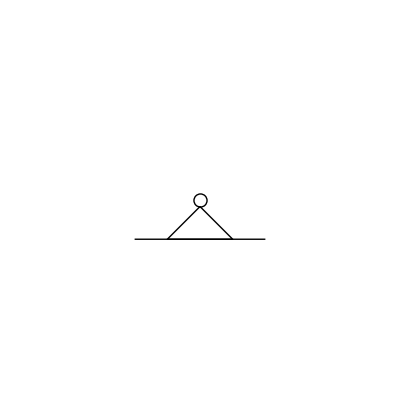

```mathematica
Linkage[{{0,0}},{PinnedJoint[1]}]
```

```mathematica
MinimizeMechanismEnergy[ Linkage[{{0,0},{1,0}},{PinnedJoint[1], RigidBar[{1,2}]}], InitialPositions->{{0,0},{2,0}}]
```

{0.,{{0.,0.},{1.,0.}}}

When more than one position is listed, those initial positions are minimized one at a time and returned as an association specifying whether an error occured, the final energy, and the final vertex coordinates after minimization.

```mathematica
MinimizeMechanismEnergy[ Linkage[{{0,0},{1,0}},{PinnedJoint[1], RigidBar[{1,2}]}], 
InitialPositions->{
{{0,0},{2,0}},
{{0,0},{1/2,0}},
{{0,0},{3,0}}
}
]
```

<|Error→{False,False,False},Energy→{0.,1.11805×10^-24,1.78039×10^-17},VertexCoordinates→{{{0.,0.},{1.,0.}},{{0.,0.},{1.,0.}},{{0.,0.},{1.,0.}}}|>

## Examples

## basic examples

### building new frameworks

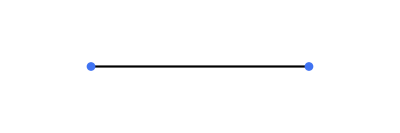

```mathematica
f=Linkage[{{0,0},{1,0}},{RigidBar[{1,2}]}]
```

There are two formats:

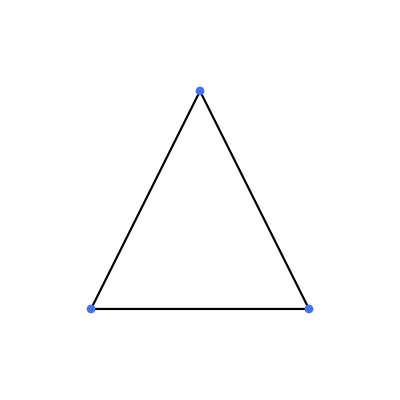

```mathematica
AddCells[ f,  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ]
```

```mathematica
AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ f
```

-Graphics-

This version allows constructions by sequential composition

#### Henneberg operations

```mathematica
?Henneberg
```

```mathematica
f2=Henneberg[2][ {1,2,"b"}, "a"->{1,1/2} ] @ Henneberg[1][ {1,2}, "c"->{1/2,-1/2} ] @ AddCells[  { FreeJoint[ "b" -> {1/2,1}], RigidBar[{1,"b"}], RigidBar[{2,"b"}]} ] @ f
```

-Graphics-

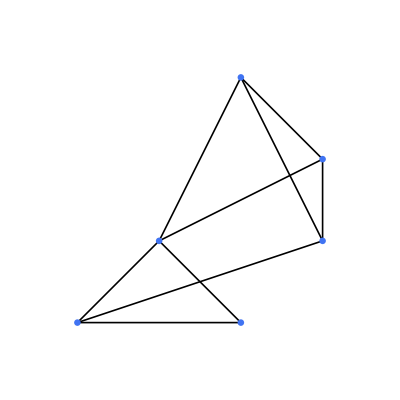

```mathematica
Henneberg[2][{-1/2,-1/2}] @ f2
```

### special mechanism examples

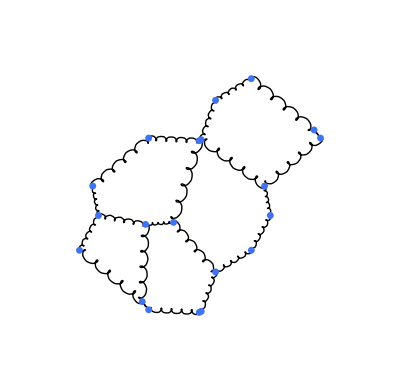

```mathematica
RandomCellNetwork[5]
```

```mathematica
m=SingleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]
```

SingleVertex[{π/4,(3 π)/4,(3 π)/4,π/4}]

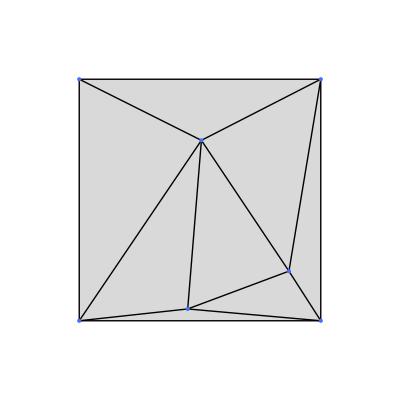

```mathematica
RandomOrigami[3]
```

```mathematica
Linkage["Examples"]
```

{PinnedFourBarLinkage,PolygonalLinkage,ChainLinkage,WattLinkage,ConnellyServatiusLinkage,Connelly2ndOrderRigidLinkage.PeaucellierLinkage}

```mathematica
?PinnedFourBarLinkage
```

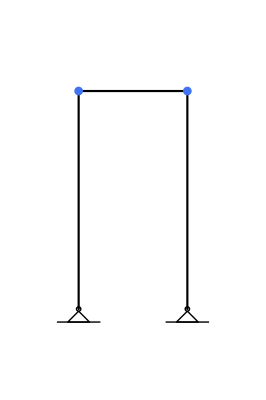

```mathematica
Linkage[PinnedFourBarLinkage[{1/2,1}]]
```

```mathematica
Origami["Examples"]
```

{BirdsFoot,SingleVertex,RandlettBirdOrigami,WaterBombBase,MiuraOriCell,SteffanPolyhedron}

```mathematica
?WaterBombBase
```

## mechanism examples

```mathematica
Linkage["Examples"]
```

{PinnedFourBarLinkage,PolygonalLinkage,ChainLinkage,WattLinkage,ConnellyServatiusLinkage,Connelly2ndOrderRigidLinkage.PeaucellierLinkage}

```mathematica
Origami["Examples"]
```

{BirdsFoot,SingleVertex,RandlettBirdOrigami,WaterBombBase,MiuraOriCell,SteffanPolyhedron}

### Watt mechanism

```mathematica
?WattLinkage
```

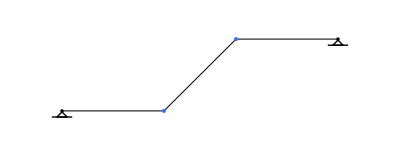

```mathematica
wattMechanism=Linkage[WattLinkage]
```

```mathematica
im=MechanismInfinitesimalMotions[ wattMechanism ,OutputVariables -> v ]
```

{{{0,0},{0,v[1]/(√2)},{0,v[1]/(√2)},{0,0}},{},{}}

```mathematica
direction = D[im[[1]],v[1]]
```

{{0,0},{0,1/(√2)},{0,1/(√2)},{0,0}}

```mathematica
MechanismZeroModes[wattMechanism]
```

{{{0,0},{0,1},{0,1},{0,0}}}

```mathematica
trajectory = MechanismIsometricTrajectory[ wattMechanism, direction, 100 ];
```

```mathematica
(*The center of the middle bar position *)
centerTrace = Mean /@ trajectory[[All, {2,3}]] ;
centerTrail = Table[ centerTrace[[1;;i]], {i,1,Length[centerTrace]}];
```

```mathematica
ListAnimate @ 
MapThread[
Show[#1,Graphics[{Blue,Point[#2]}]]&,
{
PlotMechanism[ wattMechanism, trajectory ],
centerTrail
}
]
```

### origami bird’s foot vertex

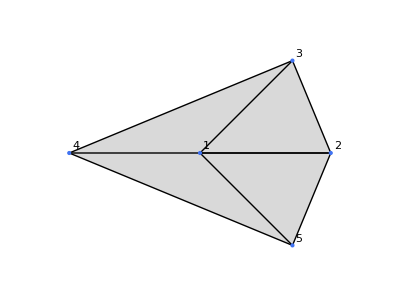

```mathematica
ChangeCellData[_FreeJoint , "Label"->"Index"]@(o=AddCells[ { Property[ TorsionalFold[{1,2}] ,  "Angle"-> Pi/2 ] } ] @Origami[BirdsFoot])
```

```mathematica
{en, pos } = MinimizeMechanismEnergy[o]
```

{3.29209×10^-19,{{-0.0132279,-0.00268693,-0.179819},{0.984348,-0.00206791,-0.2494},{0.726203,0.503991,0.263486},{-1.0108,-0.00330596,-0.110239},{0.727694,-0.49593,0.275972}}}

```mathematica
PlotMechanism[o,pos]
```

-Graphics3D-

```mathematica
{ linear, quadratic, ss} = FullSimplify[
MechanismInfinitesimalMotions[o =Origami[ SingleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]], Constraints->{VertexDisplacement[1,All[3]], VertexDisplacement[2,"z"], VertexDisplacement[3,{"x","z"}]} ,
OutputVariables -> v]
]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,v[2]},{0,0,v[1]}},{-(v[2] (√2 v[1]+v[2]))/(2 √3)},{{1/6 (√3-√6),1/(2 √6),-1/(√6),1/(2 √6),-(1+√2)/(2 √3),1/(2 √6),-1/(√6),1/(2 √6),0,0,0,0,0,0}}}

```mathematica
dir = D[ linear /. Solve[quadratic==0,{v[1],v[2]}] /. {v[1]->v,v[2]->v},v]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0},{0,0,-√2},{0,0,1}}}

```mathematica
trajectory1 = Join[
Reverse @MechanismIsometricTrajectory[ o, -dir[[1]],180,Constraints -> EuclideanMotionConstraints[{1,2,3}],StepSize -> 0.02][[All,{4,5},3]]

,
 MechanismIsometricTrajectory[ o, dir[[1]],180,Constraints ->   EuclideanMotionConstraints[{1,2,3}], StepSize-> 0.02][[All,{4,5},3]]
];

trajectory2 = Join[
Reverse @MechanismIsometricTrajectory[ o, -dir[[2]],180,Constraints ->   EuclideanMotionConstraints[{1,2,3}], StepSize -> 0.02][[All,{4,5},3]]

,
 MechanismIsometricTrajectory[ o, dir[[2]],180,Constraints ->  EuclideanMotionConstraints[{1,2,3}], StepSize -> 0.02][[All,{4,5},3]]
];
```

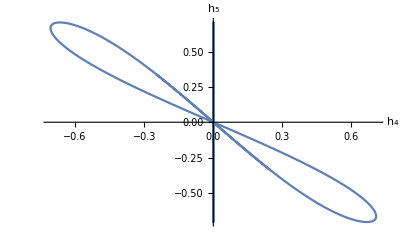

```mathematica
Show[
ListPlot[trajectory1,Joined->True],
ListPlot[trajectory2, Joined->True],

PlotRange->All,AxesLabel->{Subscript["h",4],Subscript["h",5]}
]
```

### Connelly’s example of a 2nd order rigid mechanism that is not prestress stable

The following example comes from Example 5.3.1 in Connelly, SIAM J. Discrete Math., 9, 453-491 (1996)

This 3D framework is second-order rigid but not prestress stable. Vertex 2 is on top of 7 and vertex 4 is on top of 8. To avoid identifying these two pairs of vertices with each other, we will add a small displacement to vertices 7 and 8. We define pos below for the correct vertex positions.

```mathematica
m=Linkage[{
{0,0,0},{0,1,0},{0,0,1},
{1,0,0},{1,1,0},{0,1+0.01,0},{1+0.01,0,0}
},{
RigidBar[{
{1,2},{1,3},{1,4},{1,6},{1,7},{2,3},{2,5},{2,7},{3,4},{3,5},{4,5},{4,6},{5,6},{5,7},{6,7}
},"Shape"->RigidBarShape["Width"->0.003]],
PinnedJoint[1],
Property[PinnedJoint[2],"ConstraintFunction"->(#[[{1,3}]]&) ],Property[PinnedJoint[3],"ConstraintFunction"->(#[[1]]&)]
}
]
pos={{0,0,0},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,0},{1,0,0}};
```

-Graphics3D-

There are two self stresses and two zero modes

```mathematica
ss=MechanismSelfStresses[Deformed[m,pos]]
zm=MechanismZeroModes[Deformed[m,pos]]
```

{{-1,0,0,1,0,0,-1,1,0,0,0,0,1,0,-1,0,0,0,0,0,0},{-1,0,1,1,-1,0,-1,1,0,0,1,-1,1,-1,0,0,0,0,0,0,0}}

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,0,0}}}

The linear zero modes and quadratic constraints associated with them.

```mathematica
eq=MechanismInfinitesimalMotions[PlaceVertices[m,pos],OutputVariables->v]
```

{{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,v[2]},{0,0,v[1]}},{√(2/3) v[1] v[2]+v[2]^2/(√6),-√(6/35) v[1]^2-√(10/21) v[1] v[2]+v[2]^2/(√210)},{{-1/(√6),0,0,1/(√6),0,0,-1/(√6),1/(√6),0,0,0,0,1/(√6),0,-1/(√6),0,0,0,0,0,0},{-1/(√210),0,√(6/35),1/(√210),-√(6/35),0,-1/(√210),1/(√210),0,0,√(6/35),-√(6/35),1/(√210),-√(6/35),√(5/42),0,0,0,0,0,0}}}

The system is second order rigid.

```mathematica
Solve[eq[[2]]==0,{v[1],v[2]}]
```

{{v[1]→0,v[2]→0},{v[1]→0,v[2]→0}}

There is no linear combination of the two quadratic forms that is positive definite. This is equivalent to the mechanism not being prestress stable.

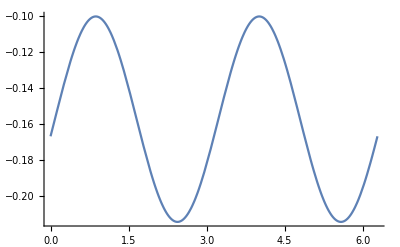

```mathematica
(*turn quadratic constraints into a matrix*)
mat=Map[
Normal@CoefficientArrays[#,{v[1],v[2]},Symmetric->True][[3]]&,
(*delete trivially zero equations first*)DeleteCases[eq[[2]],0]
];
Plot[Det[Cos[t] mat[[1]]+Sin[t] mat[[2]]],{t,0,2Pi}]
```

```mathematica
?PrestressStability
```

```mathematica
PrestressStability[m]
```

{0.,{-0.395421,1.21431×10^-17,-0.0522226,0.391506,0.0517055,-1.65831×10^-16,-0.399375,0.395421,-5.74335×10^-17,1.84004×10^-16,-0.0527448,0.0522226,0.399942,0.0567442,-0.447688,4.43533×10^-16,6.5969×10^-16,-6.46204×10^-16,-1.13423×10^-17,-3.82979×10^-16,-8.08553×10^-17}}

```mathematica
?PrestressStableQ
```

```mathematica
PrestressStableQ[m]
```

False

### Connelly and Servatius’ example of a cusp mechanism

Connelly, R. and Servatius, H., 1994. Higher-order rigidity—What is the proper definition?. Discrete & Computational Geometry, 11(2), pp.193-200.

This is an example of a mechanism that is 3rd order rigid but still has a nontrivial flex. It is constructed from two Watt linkages with equal length bars (which are highlighted below in two different colors).

```mathematica
mA=ChangeCellData[RigidBar,{{1,2},{2,3},{3,4},{4,5}},"Style"->Red]@Linkage[{{-3,0},{-2,0},{-2+1/Sqrt[2]/2,0+1/Sqrt[2]/2},{-2+1/Sqrt[2],0+1/Sqrt[2]},{-1+1/Sqrt[2],1/Sqrt[2]},{-2,1/Sqrt[2]}},{
PinnedJoint[{1,5}],RigidBar[{{1,2},{2,3},{3,4},{4,5},{4,6},{3,6},{2,6}}],
FreeJoint["a"->{-2+1/Sqrt[2]/2,0+1/Sqrt[2]/2}]
}
];
mB=ChangeCellData[RigidBar,{{1,2},{2,3},{3,4},{4,5}},"Style"->Blue]@Linkage[{{3,0},{2,0},{2-1/Sqrt[2]/2,0+1/Sqrt[2]/2},{2-1/Sqrt[2],0+1/Sqrt[2]},{1-1/Sqrt[2],1/Sqrt[2]},{2,1/Sqrt[2]}},{
PinnedJoint[{1,5}],RigidBar[{{1,2},{2,3},{3,4},{4,5},{4,6},{3,6},{2,6}}],
FreeJoint["b"->{2-1/Sqrt[2]/2,0+1/Sqrt[2]/2}]
}
];
```

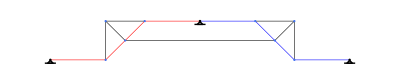

```mathematica
m=AddCells[JoinMechanism[(#+{1-1/Sqrt[2],0})& /@ mA,(#+{-1+1/Sqrt[2],0})& /@ mB],RigidBar[{"a","b"}]]
```

This is a brief animation of the motion.

```mathematica
ListAnimate[PlotMechanism[m,MechanismIsometricTrajectory[m,ReplacePart[ConstantArray[{0,0},m["VertexCount"]],4->{0,-1}],50]]]
```

```mathematica
ListAnimate[PlotMechanism[m,MechanismIsometricTrajectory[m,ReplacePart[ConstantArray[{0,0},m["VertexCount"]],10->{0,-1}],50]]]
```

At second order, the mechanism has a degenerate second order flex.

```mathematica
{lin,quad,ss}=FullSimplify@MechanismInfinitesimalMotions[m,OutputVariables->v]
```

{{{0,0},{0,v[2]/2},{0,v[2]/2},{0,v[2]/2},{0,0},{0,v[2]/2},{0,0},{0,v[1]/2},{0,v[1]/2},{0,v[1]/2},{0,v[1]/2}},{-(v[1]-v[2])^2/(2 √(238+104 √2))},{{-7/(2 √(655-8 √2)),-√((2 (655+8 √2))/8753),1/(√(26+8/(4+√2)^2)),0,-√((2 (655+8 √2))/8753),-2/(√(238+104 √2)),7/(2 √(655-8 √2)),1/(√(26+8/(4+√2)^2)),-7/(2 √(655-8 √2)),-√((2 (655+8 √2))/8753),1/(√(26+8/(4+√2)^2)),0,-√((2 (655+8 √2))/8753),7/(2 √(655-8 √2)),1/(√(26+8/(4+√2)^2)),-7/(√(655-8 √2)),0,0,0,7/(√(655-8 √2)),0}}}

```mathematica
Solve[quad==0,v[1]]
```

{{v[1]→v[2]},{v[1]→v[2]}}

```mathematica
Eigensystem[D[D[quad[[1]],{{v[1],v[2]}}],{{v[1],v[2]}}]]
```

{{-√(2/(119+52 √2)),0},{{-1,1},{1,1}}}

## periodic mechanisms

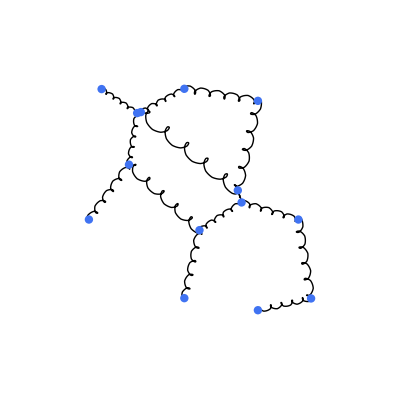

```mathematica
m=MechanismUnitCell[ m0=RandomCellNetwork[5], {{1,0},{0,1}}]
```

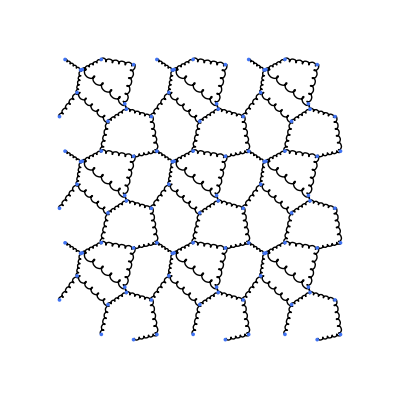

```mathematica
TesselateMechanism[ m , {{1,0},{0,1}},{3,3}]
```

```mathematica
pi=PeriodicIdentification[ m,  {{1,0},{0,1}} ]
```

PeriodicIdentificationData[V = 10
{{1,0},{0,1}}]

```mathematica
MechanismConstraintMatrix[m, Constraints -> pi["Constraints"], ReduceLinearConstraints->True ]
```

SparseArray[…]

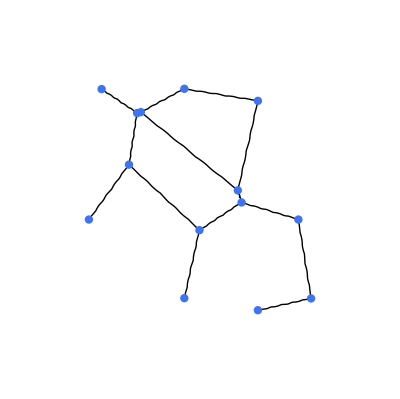

```mathematica
m2=ChangeCellData[m, _Spring ,  "EquilibriumLength" -> 0.05]
```

```mathematica
{en, pos} = MinimizeMechanismEnergy[m2, Constraints -> pi["Constraints"],MaxIterations->10^4]
```

{298.081,{{0.400691,0.0823644},{0.494778,0.273462},{0.325792,0.386519},{0.231706,0.195421},{0.467761,-0.197755},{0.258722,-0.333362},{0.325792,-0.613481},{0.494778,-0.726538},{0.742021,-0.650929},{0.734031,-0.345056},{-0.0155373,0.119812},{-0.00754802,-0.186061},{-0.265969,-0.345056},{-0.257979,0.349071}}}

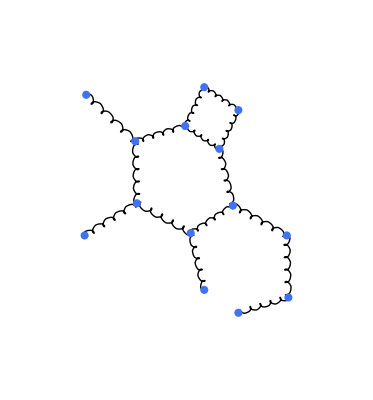

```mathematica
PlotMechanism[ m, pos ]
```

You can use Groebner bases to write constraints that allow unit cells sizes to change.

```mathematica
basis=GroebnerBasis[pi["LatticeVectors"->{{a,0},{0,b}} (*no shear deformation*)]["Constraints"],{a,b}];
basis[[1;;-3]]
```

{VertexPosition[10,y]-VertexPosition[13,y],-VertexPosition[9,x]+VertexPosition[10,x]-VertexPosition[13,x]+VertexPosition[14,x],VertexPosition[2,y]-VertexPosition[8,y]+VertexPosition[9,y]-VertexPosition[14,y],VertexPosition[2,x]-VertexPosition[8,x],VertexPosition[3,y]-VertexPosition[7,y]+VertexPosition[9,y]-VertexPosition[14,y],VertexPosition[3,x]-VertexPosition[7,x]}

The unit cell sizes are determined by

```mathematica
basis[[-2;;-1]]
```

{b+VertexPosition[9,y]-VertexPosition[14,y],a-VertexPosition[9,x]+VertexPosition[14,x]}